```mathematica
Clear["Global`*"]
```

{{0.,1},{0.1,1.21},{0.2,1.41003},{0.3,1.59798},{0.4,1.77187},{0.5,1.92982},{0.6,2.0701},{0.7,2.19112},{0.8,2.2915},{0.9,2.37002},{1.,2.42568}}

{{x[t]→Cos[t]+2 Sin[t]}}

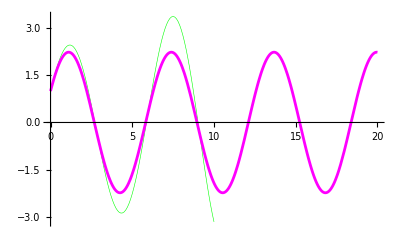

Heun[0.1,10,1,2]

{{x[t]→Cos[t]+2 Sin[t]}}

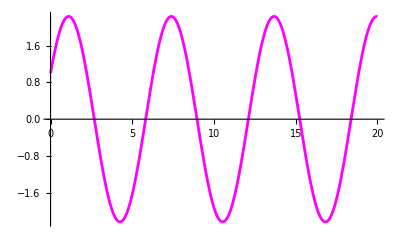

```mathematica
f[x_,t_]:=-x;
f1[x1_,x2_,t_]:= x2;
f2[x1_,x2_,t_]:= -x1;

(*Error message*)
Heun::nonnegativeint = "Nmax must be a non-negative integer";

Heun[dt_,Nmax_,a1_,a2_]:= Module[{j = 0,n,g1,g2,h1,h2,x1,x2,t},If[Or[Nmax≤ 0,Not[IntegerQ[Nmax]]],Message[Heun::nonnegativeint],x1[0]:=a1;x2[0]:= a2;
g1[j_]:=(g1[j]=f1[x1[j],x2[j],t]);
g2[j_]:=(g2[j]=f1[x1[j]+dt g1[j],x2[j]+dt g1[j],t+dt]);
h1[j_]:=(h1[j]=f2[x1[j],x2[j],t]);h2[j_]:=(h2[j]=f2[x1[j]+dt h1[j],x2[j]+dt h1[j],t+dt]);
x1[j_] := (x1[j] =x1[j-1]+ dt/2(g1[j-1] +g2[j-1]));

x2[j_] := (x2[j] = x2[j-1]+dt/2(h1[j-1] + h2[j-1]));Table[{j dt,x1[j]},{j,0,Nmax}]
]
];
Heun[.1,10,1,2]
Heungraph[dt_,Nmax_,a1_,a2_]:= ListLinePlot[Heun[dt,Nmax,a1,a2],PlotStyle->{Thickness[0.001],RGBColor[0,1,0]},PlotRange->All];

asol[a1_,a2_] := DSolve[{x''[t] == f[x[t],t],x[0] == a1,x'[0] == a2},x[t],t];

asol[1,2]

agraph[a1_,a2_,tlast_]:= Plot[Evaluate[x[t]/.asol[a1,a2]],{t,0,tlast},PlotStyle->{Thickness[0.005],RGBColor[1,0,1]},PlotRange->All];

Show[Heungraph[.1,100,1,2],agraph[1,2,20]]
```

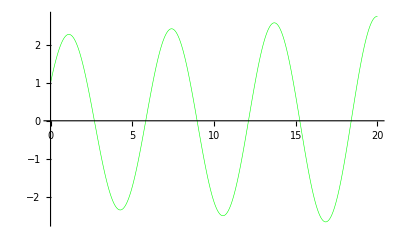

```mathematica
Heungraph[dt_,Nmax_,a1_,a2_]:= ListLinePlot[Heun[dt,Nmax,a1,a2],PlotStyle->{Thickness[0.001],RGBColor[0,1,0]},PlotRange->All];
Heungraph[.02,1000,1,2]
```

```mathematica
asol[a1_,a2_] := DSolve[{x''[t] == f[x[t],t],x[0] == a1,x'[0] == a2},x[t],t];

asol[1,2]

agraph[a1_,a2_,tlast_]:= Plot[Evaluate[x[t]/.asol[a1,a2]],{t,0,tlast},PlotStyle->{Thickness[0.005],RGBColor[1,0,1]},PlotRange->All];agraph[1,2,20]
```

{{x[t]→Cos[t]+2 Sin[t]}}

-Graphics-

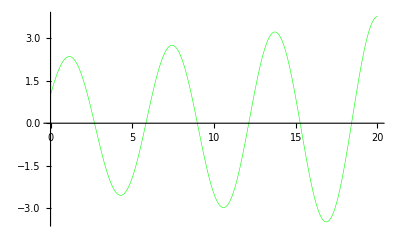

```mathematica
Heungraph[.05,400,1,2]
```

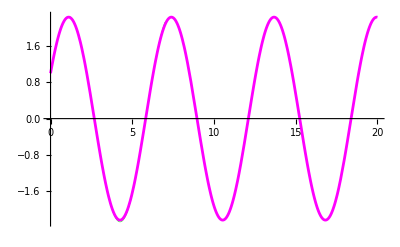

```mathematica
Show[Heungraph[.007,1000,1,2],agraph[1,2,20]]
```